```mathematica
(* Testing Quadratic Formulations *)
```

```mathematica
X=Table[Subscript[x, i],{i,1,5}];
Phi=Table[X,{i,1,Length[X]}];
Phi//MatrixForm
Z={
{1,0,0},
{1,0,0},
{0,1,0},
{0,1,0},
{0,0,1}
};
Z//MatrixForm
L=DiagonalMatrix[{1/2,1/2,1}];
L//MatrixForm
```

(x_1 | x_2 | x_3 | x_4 | x_5
x_1 | x_2 | x_3 | x_4 | x_5
x_1 | x_2 | x_3 | x_4 | x_5
x_1 | x_2 | x_3 | x_4 | x_5
x_1 | x_2 | x_3 | x_4 | x_5)

(1 | 0 | 0
1 | 0 | 0
0 | 1 | 0
0 | 1 | 0
0 | 0 | 1)

(1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 1)

```mathematica
M=Phi.Z.L.Transpose[Z];
M//MatrixForm
```

(1/2 (x_1+x_2) | 1/2 (x_1+x_2) | 1/2 (x_3+x_4) | 1/2 (x_3+x_4) | x_5
1/2 (x_1+x_2) | 1/2 (x_1+x_2) | 1/2 (x_3+x_4) | 1/2 (x_3+x_4) | x_5
1/2 (x_1+x_2) | 1/2 (x_1+x_2) | 1/2 (x_3+x_4) | 1/2 (x_3+x_4) | x_5
1/2 (x_1+x_2) | 1/2 (x_1+x_2) | 1/2 (x_3+x_4) | 1/2 (x_3+x_4) | x_5
1/2 (x_1+x_2) | 1/2 (x_1+x_2) | 1/2 (x_3+x_4) | 1/2 (x_3+x_4) | x_5)

```mathematica
A=(Phi-M).Transpose[Phi-M]//FullSimplify;
A//MatrixForm
```

(1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2)
1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2)
1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2)
1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2)
1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2) | 1/2 ((x_1-x_2)^2+(x_3-x_4)^2))

```mathematica
Tr[A]
```

5/2 ((x_1-x_2)^2+(x_3-x_4)^2)

```mathematica
((Subscript[x, 1]-Subscript[μ, 1])^2+(Subscript[x, 2]-Subscript[μ, 1])^2+(Subscript[x, 3]-Subscript[μ, 2])^2+(Subscript[x, 4]-Subscript[μ, 2])^2+(Subscript[x, 5]-Subscript[μ, 3])^2)/.{Subscript[μ, 1]->1/2(Subscript[x, 1]+Subscript[x, 2]),Subscript[μ, 2]->1/2(Subscript[x, 3]+Subscript[x, 4]),Subscript[μ, 3]->Subscript[x, 5]}//FullSimplify
```

1/2 ((x_1-x_2)^2+(x_3-x_4)^2)

```mathematica
Transpose[Z].Z//MatrixForm
```

(2 | 0 | 0
0 | 2 | 0
0 | 0 | 1)

```mathematica
K=Phi.Transpose[Phi];
K//MatrixForm
```

(x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2
x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2
x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2
x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2
x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2 | x_1^2+x_2^2+x_3^2+x_4^2+x_5^2)

```mathematica
Tr[Phi.Transpose[Phi]-Phi.Z.L.Transpose[Z].Transpose[Phi]]//FullSimplify
```

5/2 ((x_1-x_2)^2+(x_3-x_4)^2)

```mathematica
Tr[Phi.Z.L.Transpose[Z].Transpose[Phi]]//FullSimplify
```

5/2 ((x_1+x_2)^2+(x_3+x_4)^2+2 x_5^2)

```mathematica
Tr[(L^(1/2)).Transpose[Z].Transpose[Phi].Phi.Z.(L^(1/2))^]//FullSimplify
```

5/2 ((x_1+x_2)^2+(x_3+x_4)^2+2 x_5^2)

```mathematica
Transpose[Phi].Phi//MatrixForm
```

(5 x_1^2 | 5 x_1 x_2 | 5 x_1 x_3 | 5 x_1 x_4 | 5 x_1 x_5
5 x_1 x_2 | 5 x_2^2 | 5 x_2 x_3 | 5 x_2 x_4 | 5 x_2 x_5
5 x_1 x_3 | 5 x_2 x_3 | 5 x_3^2 | 5 x_3 x_4 | 5 x_3 x_5
5 x_1 x_4 | 5 x_2 x_4 | 5 x_3 x_4 | 5 x_4^2 | 5 x_4 x_5
5 x_1 x_5 | 5 x_2 x_5 | 5 x_3 x_5 | 5 x_4 x_5 | 5 x_5^2)

```mathematica
Clear[x,y,L,Z,K,X,Phi,G,H]

K[x_,y_]:=Norm[x]+Norm[y]-Norm[x-y]

TrE[Z_,K_,L_]:=Tr[(L^(1/2)).Transpose[Z].K.Z.L^(1/2)]

ShuffleZ[n_,Z_]:=(
m=Length[Z]/2;
Z1=Z[[1;;m]];
Z2=Z[[m+1;;]];
idx=RandomInteger[{1,m},n];
For[i=1,i≤Length[idx],i++,
j=idx[[i]];
a=Z1[[j]];
b=Z2[[j]];
Z1[[j]]=b;
Z2[[j]]=a;
];
Return[Join[Z1,Z2]];
)
```

```mathematica
n=500;
X1=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,2}}],n];
X2=RandomVariate[MultinormalDistribution[{5,5},{{1,0},{0,1}}],n];
X=Join[X1,X2];
Z=Join[Table[{1,0},{i,1,n}],Table[{0,1},{i,1,n}]];

H=Table[X[[i]].X[[j]],{i,1,Length[X]},{j,1,Length[X]}];
G=Table[K[X[[i]],X[[j]]],{i,1,Length[X]},{j,1,Length[X]}];
L=DiagonalMatrix[{1/n,1/n}];
```

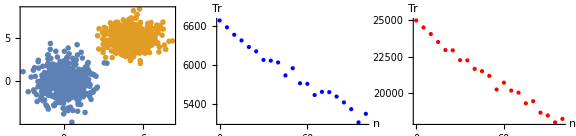

```mathematica
g1=ListPlot[{X1,X2},PlotStyle->{PointSize[.01]},Axes->False,Frame->True,AspectRatio->1];
g2=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],G,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],H,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Red,PointSize[Medium]}];
plot1=GraphicsRow[{g1,g2,g3},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\plot1.pdf",plot1,"PDF"]
```

C:\Users\guifr\Desktop\plot1.pdf

```mathematica
n=500;
X1=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],n];
X2=RandomVariate[MultinormalDistribution[{0,0},{{2,1},{1,5}}],n];
Z1=Table[{1,0},{i,1,n}];
Z2=Table[{0,1},{i,1,n}];
X=Join[X1,X2];
Z=Join[Z1,Z2];

H=Table[X[[i]].X[[j]],{i,1,Length[X]},{j,1,Length[X]}];
G=Table[K[X[[i]],X[[j]]],{i,1,Length[X]},{j,1,Length[X]}];
L=DiagonalMatrix[{1/n,1/n}];
```

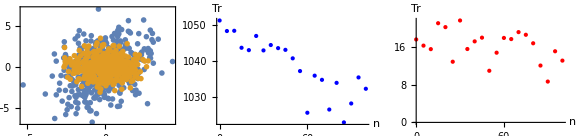

```mathematica
g1=ListPlot[{X2,X1},PlotStyle->{PointSize[.01]},Axes->False,Frame->True,AspectRatio->1];
g2=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],G,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],H,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Red,PointSize[Medium]}];
plot2=GraphicsRow[{g1,g2,g3},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\plot2.pdf",plot2,"PDF"]
```

C:\Users\guifr\Desktop\plot2.pdf

```mathematica
(* funny functions to generate data *)

G1[η_]:=(
t = RandomReal[{-1,1}];
v={10t,10 t^3+2 t^2-10t};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G2[η_]:=(
t = RandomReal[{0,4Pi}];
v={t Cos[t],t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G3[η_]:=(
t = RandomReal[{0,4Pi}];
v={3 Cos[t],3 Sin[t],3t};
v=v+η RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]];
Return[v];
)

G4[η_]:=(
t = RandomReal[{-1,1}];
v={10t+12,10 t^3+2 t^2-10t+1};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G5[η_]:=(
t = RandomReal[{0,4Pi}];
v={-t Cos[t],-t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G6[η_]:=(
t = RandomReal[{0,4Pi}];
v={-Cos[t],- Sin[t],2t};
v=v+η RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]];
Return[v];
)

G7[η_]:=(
t = RandomReal[{0,2Pi}];
v={ Cos[t], Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
```

```mathematica
n=500;
X1=Table[G1[0.1],{i,1,n}];
X2=Table[G4[0.1],{i,1,n}];
Z1=Table[{1,0},{i,1,n}];
Z2=Table[{0,1},{i,1,n}];
X=Join[X1,X2];
Z=Join[Z1,Z2];

H=Table[X[[i]].X[[j]],{i,1,Length[X]},{j,1,Length[X]}];
G=Table[K[X[[i]],X[[j]]],{i,1,Length[X]},{j,1,Length[X]}];
L=DiagonalMatrix[{1/n,1/n}];
```

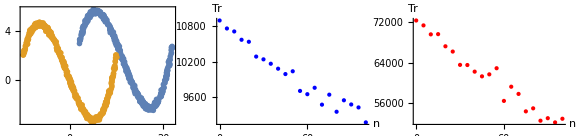

```mathematica
g1=ListPlot[{X2,X1},PlotStyle->{PointSize[.01]},Axes->False,Frame->True,AspectRatio->1];
g2=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],G,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],H,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Red,PointSize[Medium]}];
GraphicsRow[{g1,g2,g3},ImageSize->Large]
```

```mathematica
n=10;
X1=Table[G2[0.1],{i,1,n}];
X2=Table[G5[0.1],{i,1,n}];
Z1=Table[{1,0},{i,1,n}];
Z2=Table[{0,1},{i,1,n}];
X=Join[X1,X2];
Z=Join[Z1,Z2];

H=Table[X[[i]].X[[j]],{i,1,Length[X]},{j,1,Length[X]}];
G=Table[K[X[[i]],X[[j]]],{i,1,Length[X]},{j,1,Length[X]}];
L=DiagonalMatrix[{1/n,1/n}];
```

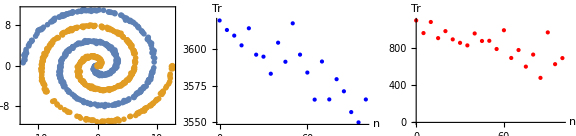

```mathematica
g1=ListPlot[{X2,X1},PlotStyle->{PointSize[.01]},Axes->False,Frame->True,AspectRatio->1];
g2=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],G,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],H,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Red,PointSize[Medium]}];
plot3=GraphicsRow[{g1,g2,g3},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\plot3.pdf",plot3,"PDF"]
```

C:\Users\guifr\Desktop\plot3.pdf

```mathematica
n=500;
X1=Table[G7[0.1],{i,1,n}];
X2=RandomVariate[MultinormalDistribution[{0,0},{{.1,0},{0,.1}}],n];
Z1=Table[{1,0},{i,1,n}];
Z2=Table[{0,1},{i,1,n}];
X=Join[X1,X2];
Z=Join[Z1,Z2];

H=Table[X[[i]].X[[j]],{i,1,Length[X]},{j,1,Length[X]}];
G=Table[K[X[[i]],X[[j]]],{i,1,Length[X]},{j,1,Length[X]}];
L=DiagonalMatrix[{1/n,1/n}];
```

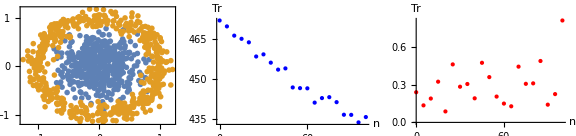

```mathematica
g1=ListPlot[{X2,X1},PlotStyle->{PointSize[.01]},Axes->False,Frame->True,AspectRatio->1];
g2=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],G,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{i,TrE[ShuffleZ[i,Z],H,L]},{i,0,100,5}],AxesLabel->{"n","Tr"},PlotStyle->{Red,PointSize[Medium]}];
plot4=GraphicsRow[{g1,g2,g3},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\plot4.pdf",plot4,"PDF"]
```

C:\Users\guifr\Desktop\plot4.pdf

```mathematica
GetZ[G_]:=(
U=Transpose[Eigenvectors[G]][[;;,1;;2]];
V=U;
For[i=1,i≤Length[U],i++,
v=Abs[U[[i]]/Norm[U[[i]]]];
vm=Max[v];
V[[i]]=Table[If[v[[k]]==vm,1,0],{k,1,Length[v]}];
];
Return[V];
)

Obj[G_,L_,Z_]:=(
t=TrE[Z,G,L];
Λ=Eigenvalues[G];
l=Sum[Λ[[i]],{i,1,Length[Λ]}];
Return[{t,l}]
)
```

```mathematica
(*
n=10;
X1=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],n];
X2=RandomVariate[MultinormalDistribution[{0.1,0.5},{{1,0},{0,5}}],n];
X=Join[X1,X2];
Z=Join[Table[{1,0},{i,1,n}],Table[{0,1},{i,1,n}]];
*)
n=10;
X1=Table[G7[0.1],{i,1,n}];
X2=RandomVariate[MultinormalDistribution[{0,0},{{.1,0},{0,.1}}],n];
Z1=Table[{1,0},{i,1,n}];
Z2=Table[{0,1},{i,1,n}];
X=Join[X1,X2];
Z=Join[Z1,Z2];


H=Table[X[[i]].X[[j]],{i,1,Length[X]},{j,1,Length[X]}];
G=Table[K[X[[i]],X[[j]]],{i,1,Length[X]},{j,1,Length[X]}];
L=DiagonalMatrix[{1/n,1/n}];

GetZ[G]//MatrixForm
GetZ[H]//MatrixForm
```

(1 | 0
0 | 1
0 | 1
0 | 1
0 | 1
0 | 1
0 | 1
1 | 0
0 | 1
1 | 0
0 | 1
1 | 0
1 | 0
1 | 0
0 | 1
1 | 0
1 | 0
1 | 0
1 | 0
1 | 0)

(1 | 0
1 | 0
0 | 1
1 | 0
1 | 0
1 | 0
1 | 0
0 | 1
1 | 0
0 | 1
1 | 0
0 | 1
0 | 1
0 | 1
1 | 0
0 | 1
0 | 1
0 | 1
1 | 0
0 | 1)